# Numerical Methods - Problem Set 6

## Problem 1

```mathematica
R00 = 2/3 h (f[0]+4 f[2]+f[4])
```

2/3 h (f[0]+4 f[2]+f[4])

```mathematica
R10 = Sum[(h/3)(f[2 i - 2] + 4 f[2 i - 1] + f[2 i]),{i, 1, 4/2}]
```

1/3 h (f[0]+4 f[1]+f[2])+1/3 h (f[2]+4 f[3]+f[4])

```mathematica
Simplify[R10]
```

1/3 h (f[0]+4 f[1]+2 f[2]+4 f[3]+f[4])

```mathematica
R11 = R10 + 1/15(R10 - R00)
```

1/3 h (f[0]+4 f[1]+f[2])+1/3 h (f[2]+4 f[3]+f[4])+1/15 (1/3 h (f[0]+4 f[1]+f[2])-2/3 h (f[0]+4 f[2]+f[4])+1/3 h (f[2]+4 f[3]+f[4]))

```mathematica
Simplify[R11]
```

2/45 h (7 f[0]+32 f[1]+12 f[2]+32 f[3]+7 f[4])

```mathematica
R11 = (16 R10 - R00)/15
```

1/15 (-2/3 h (f[0]+4 f[2]+f[4])+16 (1/3 h (f[0]+4 f[1]+f[2])+1/3 h (f[2]+4 f[3]+f[4])))

```mathematica
Simplify[R11]
```

2/45 h (7 f[0]+32 f[1]+12 f[2]+32 f[3]+7 f[4])

## Problem 2

```mathematica
f[x_]:= (2^x Sin[x])/x
```

```mathematica
xi = 0.1
xf = 1.1
```

0.1

1.1

```mathematica
Integrate[f[x],{x,xi,xf}]
```

1.41892

```mathematica
NumberForm[1.41891918440222,16]
```

1.41891918440222

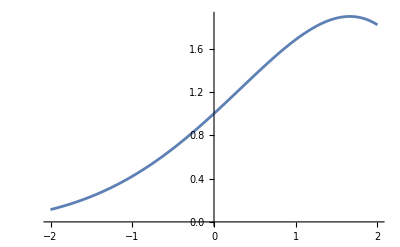

```mathematica
Plot[f[x],{x,-2,2}]
```

## a) Simpson’s 1/3 rule

```mathematica
intervals = 2
stepSize = (xf - xi)/intervals
```

2

0.5

```mathematica
xVals = {xi, xi+stepSize, xi + 2 * stepSize}
```

{0.1,0.6,1.1}

```mathematica
integralSimp = stepSize/3(f[xVals[[1]]] + 4 f[xVals[[2]]] + f[xVals[[3]]])
```

1.41871

## b) Simpson’s 1/3 rule with the Rhomberg algorithm

```mathematica
intervals = 4
stepSize = (xf - xi)/intervals
```

4

0.25

```mathematica
xVals = {xi, xi+stepSize, xi + 2 * stepSize, xi + 3 * stepSize, xi + 4 * stepSize}
```

{0.1,0.35,0.6,0.85,1.1}

```mathematica
integralRhomb = (2 stepSize)/45(7 f[xVals[[1]]] + 32 f[xVals[[2]]] + 12 f[xVals[[3]]] + 32 f[xVals[[4]]] + 7 f[xVals[[5]]])
```

1.41892